Lp (m^2*s/kg): 1.7E-10 for 2p equations with osmolality inputs versus 1.7E-13 for 2p equations with osmolarity inputs.

Ps (m/s): 6.8E-7 (for either formulation of the 2p equations)

Max concentration of CPA surrounding the sample: 2 osmolal = 1909.85 mM

Initial intracellular CPA concentration: 0 osmolal = 0. mM

Initial intracellular nonpenetrating concentration: 0.3 osmolal = 297.278 mM

Extracellular nonpenetrating concentration: 0.3 osmolal = 297.278 mM

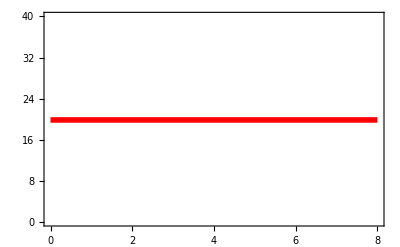
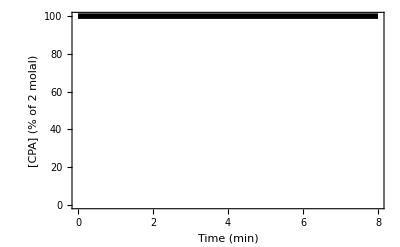
-Graphics--Graphics-CPA Exposure Profile 1

-Graphics-

```mathematica
(*Goal: Improve the simulation result by using osmolarity, with comparison to Program 2 (min V/V0 = 0.65, max V/V0 = 0.97)*)
(*Rationale: There is a unit mismatch in the v'[t] equation (as published in Kleinhans 1998). Whereas v is in units of m^3,the unconverted terms in the v'[t] equation include osomolality (whose units include kg, not m^3). Using osmolarity (whose units include m^3) would provide unit consistency.*)
(*Approach: Use the same inputs (osmolality) as in Program 2, then convert these to osmolarity and compare the result.*)
(*Other improvements: 
1. I used a 1000x lower Lp value; otherwise, the v(t) solution to the omsolarity-formulated 2p equations went negative
2. I changed the intracellular nonpenetrating concentration term from (Cn0*(V0-Vb))/v[t] to (Cn0*(V0-Vb))/(v[t]+n[t]*MVCPA) and the intracellular CPA concetration term in the 2p equations from n[t]/v[t] to n[t]/(v[t]+n[t]*MVCPA) because CPA contributes to the volume of the solution
3. I developed the program to run well for either (user choice) osmolarity or osomolality inputs (min V/V0 = 0.68 and max V/V0 = 1.0 for both)
*)
(*Note: I kept area constant in the 2p equations; I was told by Nik that this is actually a realistic assumption*)
(*Conclusions: 
1. Any extracted parameter values (for Lp and Ps) are dependent on the formulation of the 2p equations; convert these values (e.g. divide Lp by 1000) if necessary 
2. After changing to osmolarity plus Other Improvement #1 above, I got min V/V0 = 0.7 and max V/V0 = 1.07
3. After changing to osmolarity plus Other Improvement #1-2 above, I got min V/V0 = 0.68 and max V/V0 = 1.0; this is similar to the prior result using osmolality
*)

Clear["Global`*"]

(*inputs*)
profiles={
{{{100,t<8*60}},293,1}
}; (*enter in the format: {surroudning CPA concentration as a function of time (c=f(t)), temperature (T), step number of the final loading step (locLf)}*)
MVCPA=.071/1000; (*m^3/mol, molar volume of CPA, compare to 7.1E-5 m^3/mol for glycerol, compare to 7.1E-5 m^3/mol for DMSO*)
Vb=.25*V0; (*osmotically inactive cell volume, compare to .2V0 for oocytes (Newton 1999)*)
adhered=0; (*enter 1 if cell is adherent (2D), enter ≠ 1 if cell is nonadherent (3D)*)

(*concentration inputs (comment out the input type (either osmolarity or osmolality) you do not want)*)
(*osmolarity inputs*)
inputsOsmolal=0; (*recommended to set at 0; if set at 1, the program will attempt to convert osmolality inputs*)
Cmax=1.9*1000; (*osmol/m^3 = mol/m^3 (true for CPA), max molarity of CPA surrounding the sample*)
C0=0*1000;(*osmol/m^3 = mol/m^3 (true for CPA), initial intracellular CPA molarity*)
Cn0=.297*1000;(*osmol/m^3, initial intracellular nonpenetrating osmolarity*)
Cne=.297*1000;(*osmol/m^3, extracellular nonpenetrating osmolarity, compare to .332 for Celsior*)
(*osmolality inputs*)
inputsOsmolal=1; (*recommended to set at 1; any value other than 1: the program will not convert osmolality inputs to osmolarity*)
Mmax=2; (*osmol/kg, max osmolality of CPA surrounding the sample*)
M0=0; (*osmol/kg, initial intracellular CPA osmolality*)
Mn0=.3; (*osmol/kg, initial intracellular nonpenetrating osmolality, compare to .326 for porcine myocardium*)
Mne=.3; (*osmol/kg, extracellular nonpenetrating osmolality, compare to .335 for Celsior (Ostrozka-Cieslik 2009)*)

(*geometry inputs and calculations (comment out the geometry that you do not want)*)
(*(*inputs for an elliptical geometry*)
Lcell=110/1000/1000; (*m, length of cell, compare to 110 um for rat ventricular myocytes (Boyett 1991)*)
R1cell = 25/1000/1000; (*m, major radius of cell, compare to 25 um for rat ventricular myocytes (Boyett 1991)*)
RRatio=1/3; (*ratio of minor radius to major radius, compare to 1/3 for rat ventricular myocytes (Boyett 1991)*)
(*equations for an elliptical geomtery*)
R2cell=R1cell*RRatio; (*m, minor radius of cell*)
A0=π*Lcell*(R1cell+R2cell)+2*π*R1cell*R2cell; (*m^2, initial cell surface area, compare to 4.5E-6 for oocytes (Carbrey)*)
V0=π*Lcell*R1cell*R2cell/4; (*m^3, initial cell volume*)*)
(*inputs for a spherical geometry*)
Dcell=100/1000/1000; (*m, cell diameter, compare to 20 um for mostly-detached D13 hiPSC-CM (my measurement)*)
(*equations for a spherical geometry*)
A0=π*Dcell^2; (*m^2, initial cell surface area, compare to 4.5E-6 for oocytes (Carbrey)*)
V0=π*Dcell^3/6; (*m^3, initial cell volume*)

(*parameters*)
LpOsmolal=1.05/1000/60/101325; (*m^2*s/kg = m/s/Pa*)
Lp=LpOsmolal/1000; (*m^2*s/kg*)
Print["Lp (m^2*s/kg): "<>ToString[Round[10*MantissaExponent[LpOsmolal][[1]],.1]]<>"E"<>ToString[MantissaExponent[LpOsmolal][[2]]-1]<>" for 2p equations with osmolality inputs versus "<>ToString[Round[10*MantissaExponent[Lp][[1]],.1]]<>"E"<>ToString[MantissaExponent[Lp][[2]]-1]<>" for 2p equations with osmolarity inputs."];
Ps=.00406/100/60; (*m/s*)
Print["Ps (m/s): "<>ToString[Round[10*MantissaExponent[Ps][[1]],.1]]<>"E"<>ToString[MantissaExponent[Ps][[2]]-1]<>" (for either formulation of the 2p equations)"]

(*constants*)
Rgas=8.3145; (*J/mol/K = N*m/mol/K = kg*m^2/mol/K/s^2, gas constant*)

(*convert to osmolarity if necessary*)
If[inputsOsmolal==1,
Mw=55.55; (*mol water/kg water*)
Cw=55.346; (*mol water/L water*)
Cmax=1000*Mmax*(Cw-Mne-Mmax)/Mw; (*osmol/m^3 = mol/m^3 (true for CPA), max molarity of CPA surrounding the sample*)
Print["Max concentration of CPA surrounding the sample: "<>ToString[Mmax]<>" osmolal = "<>ToString[Cmax]<>" mM"];
C0=1000*M0*(Cw-Mn0-M0)/Mw;(*osmol/m^3 = mol/m^3 (true for CPA), initial intracellular CPA molarity*)
Print["Initial intracellular CPA concentration: "<>ToString[M0]<>" osmolal = "<>ToString[C0]<>" mM"];
Cn0=1000*Mn0*(Cw-Mn0-M0)/Mw; (*osmol/m^3, initial intracellular nonpenetrating osmolarity*)
Print["Initial intracellular nonpenetrating concentration: "<>ToString[Mn0]<>" osmolal = "<>ToString[Cn0]<>" mM"];
Cne=1000*Mne*(Cw-Mne)/Mw; (*osmol/m^3, extracellular nonpenetrating osmolarity*)
Print["Extracellular nonpenetrating concentration: "<>ToString[Mn0]<>" osmolal = "<>ToString[Cn0]<>" mM"];
];

(*equations*)
If[adhered==1, (*if cell is adhered*)
A0=A0/2; (*assume half the cell membrane is exposed*)
]

(*initialization*)
VPlots={};
colors={Blue,Green,Black, Red,Purple,Orange,Brown,Yellow};
table={{"Profile","Max C_e (M)","T (°C)","t_tot (min)","Min V/V_0","Max V/V_0"}};

(*execution*)
nProfiles=Length[profiles];
ttotmax=Max[profiles[[All,1]][[All,-1]][[All,2,2]]];
For[i=1,i<nProfiles+1,i++,
If[inputsOsmolal==1,(*if concentration unit is osmolality*)
Me=Piecewise[profiles[[i]][[1]]]*Mmax/100; (*mol/m^3 = mM, c=f(t)*)
Ce=1000*Me*(Cw-Mne-Me)/Mw; (*osmol/m^3 = mol/m^3 (true for CPA), extracellular CPA molarity*)
,(*if concentration unit is osmolarity*)
Ce=Piecewise[profiles[[i]][[1]]]*Cmax/100; (*mol/m^3 = mM, c=f(t)*)
];
T=profiles[[i]][[2]]; (*K, T=f(t)*)
locLf=profiles[[i]][[3]]; (*location of the final loading step*)
nSteps=Length[profiles[[i]][[1]]];(*number of c steps*)
ttot=Last[profiles[[i]][[1]]][[2,2]]; (*s, total simulation time*)
vnSol=NDSolve[{v'[t]==-Lp*A0*Rgas*T*(Cne+Ce-(Cn0*(V0-Vb))/(v[t]+n[t]*MVCPA)-n[t]/(v[t]+n[t]*MVCPA)),n'[t]==Ps*A0*(Ce-n[t]/(v[t]+n[t]*MVCPA)),v[0]==V0-Vb,n[0]==C0*(V0-Vb)},{v,n},{t,0,ttot},MaxStepSize->.1][[1]];
v[t_]:=Evaluate[v[t]/.vnSol[[1]]]; (*m^3, volume of intracellular water*)
n[t_]:=Evaluate[n[t]/.vnSol[[2]]];(*osmol = mol (equation true for CPA), amount of intracellular CPA*)
Vr[n_,v_]:=(v+MVCPA*n+Vb)/V0;(*ratio of cell volume to initial cell volume*)
(*initialization*)
Vmins={}; (*list of Vmin for each step*)
Vmaxs={}; (*list of Vmax for each step*)
tPriorSteps=0; (*s, time of all prior steps*)
For[j=1,j<nSteps+1,j++,
tCurrentStep=profiles[[i]][[1]][[j]][[2,2]]; (*s, time until the end of the current step*)
If[j≤locLf,(*if this is a loading step*)
AppendTo[Vmins,FindMinimum[{Vr[n[t],v[t]],tPriorSteps<t<tCurrentStep},t][[1]]];
,(*if this is an unloading step*)
AppendTo[Vmaxs,FindMaximum[{Vr[n[t],v[t]],tPriorSteps<t<tCurrentStep},t][[1]]];
];
tPriorSteps=tCurrentStep;
];
Vmin=If[Length[Vmins]>0,Min[Vmins],Min[{Vr[n[0],v[0]],Vr[n[ttot],v[ttot]]}]];
Vmax=If[Length[Vmaxs]>0,Max[Vmaxs],Max[{Vr[n[0],v[0]],Vr[n[ttot],v[ttot]]}]];
Ce=Ce/.t->t*60; (*for plotting in min*)
Print[Labeled[Overlay[{Plot[T-273.15,{t,0,ttot/60},PlotStyle->{Red,Thickness[.01]},ImagePadding->{{45,45},{45,5}},PlotRange->{0,40},Frame->{False,False,False,True},FrameTicks->{{None,All},{None,None}},FrameStyle->{Automatic,Automatic,Automatic,Red},FrameLabel->{{None,"T (°C)"},{None,None}}],Plot[Floor[Ce*100/Cmax,.1],{t,0,ttot/60},PlotStyle->{Black,Thickness[.01]},ImagePadding->{{45,45},{45,5}},PlotRange->{0,100},Frame->{True,True,False,False},FrameStyle->{Automatic,Black,Automatic,Automatic},FrameLabel->{{If[inputsOsmolal==1,"[CPA] (% of "<>ToString[NumberForm[Mmax,2]]<>" molal)","[CPA] (% of "<>ToString[NumberForm[Cmax/1000,2]]<>" M)"],None},{"Time (min)",None}}]}],"CPA Exposure Profile "<>ToString[i],Top]];
If[i<nProfiles,(*if this is not the last profile*)
AppendTo[VPlots,Plot[Vr[n[t*60],v[t*60]],{t,0,ttotmax/60},PlotRange->{0,Ceiling[1.1*Vmax,.1]},AxesLabel->{"t (min)","V/V_0"},PlotStyle->colors[[i]]]];
,(*if this is the last profile*)
AppendTo[VPlots,Plot[Vr[n[t*60],v[t*60]],{t,0,ttotmax/60},PlotRange->{0,Ceiling[1.1*Vmax,.1]},AxesLabel->{"t (min)","V/V_0"},PlotStyle->colors[[i]],PlotLegends->Placed[LineLegend[colors,Range[nProfiles],LegendLabel->"Profile",LegendFunction->Framed],{1,.6}]]];
];
AppendTo[table,{i,Round[Cmax/1000,.1],Round[T-273.15,.1],ttot/60,Round[Vmin,.01],Round[Vmax,.01]}];
Clear[v,n];
]; (*end of i loop*)
Show[VPlots]
Dataset[AssociationThread[First@table->#]&/@Rest@table]
```